```mathematica
state20 = Import["/Users/andrewross/Documents/Euler1D/Euler1D/density_12_(cells=20)_(CFL=0.010000).txt", "Table"];
error20= (Sum[(Exactρ[state20⟦i,1⟧, 0.014] - state20⟦i,2⟧)^2, {i, 1, Length[state20]}]/Length[state20])^(1/2);

state40 = Import["/Users/andrewross/Documents/Euler1D/Euler1D/density_12_(cells=40)_(CFL=0.010000).txt", "Table"];
error40= (Sum[(Exactρ[state40⟦i,1⟧, 0.014] - state40⟦i,2⟧)^2, {i, 1, Length[state40]}]/Length[state40])^(1/2);

state80 = Import["/Users/andrewross/Documents/Euler1D/Euler1D/density_12_(cells=80)_(CFL=0.010000).txt", "Table"];
error80= (Sum[(Exactρ[state80⟦i,1⟧, 0.014] - state80⟦i,2⟧)^2, {i, 1, Length[state80]}]/Length[state80])^(1/2);

state160 = Import["/Users/andrewross/Documents/Euler1D/Euler1D/density_12_(cells=160)_(CFL=0.010000).txt", "Table"];
error160= (Sum[(Exactρ[state160⟦i,1⟧, 0.014] - state160⟦i,2⟧)^2, {i, 1, Length[state160]}]/Length[state160])^(1/2);

state320 = Import["/Users/andrewross/Documents/Euler1D/Euler1D/density_12_(cells=320)_(CFL=0.010000).txt", "Table"];
error320= (Sum[(Exactρ[state320⟦i,1⟧, 0.014] - state320⟦i,2⟧)^2, {i, 1, Length[state320]}]/Length[state320])^(1/2);

state640 = Import["/Users/andrewross/Documents/Euler1D/Euler1D/density_12_(cells=640)_(CFL=0.010000).txt", "Table"];
error640= (Sum[(Exactρ[state640⟦i,1⟧, 0.014] - state640⟦i,2⟧)^2, {i, 1, Length[state640]}]/Length[state640])^(1/2);
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
type = "24";
error20 = {20, Import["/Users/andrewross/Documents/Euler1D/Euler1D/error_"<>type<>"_(cells=20)_(CFL=0.010000).txt", "Table"]⟦1,1⟧};
error40 = {40, Import["/Users/andrewross/Documents/Euler1D/Euler1D/error_"<>type<>"_(cells=40)_(CFL=0.010000).txt", "Table"]⟦1,1⟧};
error80 = {80, Import["/Users/andrewross/Documents/Euler1D/Euler1D/error_"<>type<>"_(cells=80)_(CFL=0.010000).txt", "Table"]⟦1,1⟧};
error160 = {160, Import["/Users/andrewross/Documents/Euler1D/Euler1D/error_"<>type<>"_(cells=160)_(CFL=0.010000).txt", "Table"]⟦1,1⟧};
error320 = {320, Import["/Users/andrewross/Documents/Euler1D/Euler1D/error_"<>type<>"_(cells=320)_(CFL=0.010000).txt", "Table"]⟦1,1⟧};
error640 = {640, Import["/Users/andrewross/Documents/Euler1D/Euler1D/error_"<>type<>"_(cells=640)_(CFL=0.010000).txt", "Table"]⟦1,1⟧};
ListLogLogPlot[{error20, error40, error80, error160, error320, error640}, Joined->True]
```

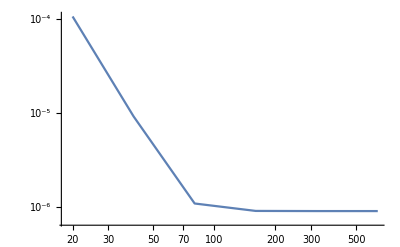

```mathematica
4
```

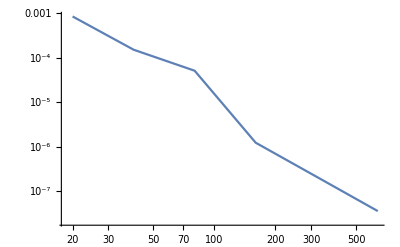

```mathematica
3
```

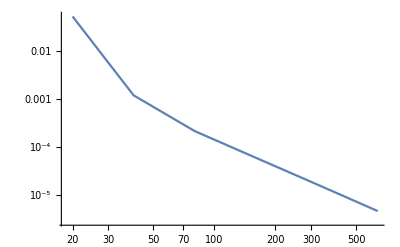

```mathematica
2
```

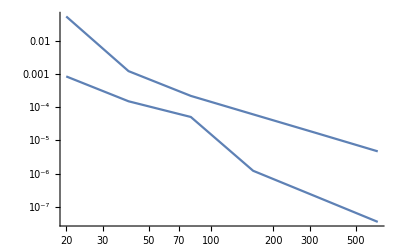

```mathematica
Show[-Graphics-,-Graphics-, PlotRange-> All]
```

```mathematica
3100 - 2822.33
```

277.67

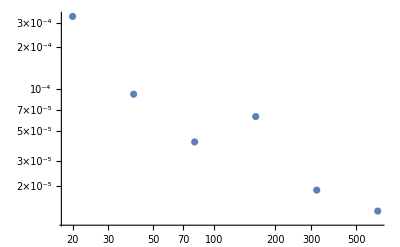

```mathematica
ListLogLogPlot[{error20, error40, error80, error160, error320, error640}]
```

```mathematica
Import["/Users/andrewross/Documents/Euler1D/Euler1D/error_12_(cells=20)_(CFL=0.010000).txt", "Table"]
```

{{0.000332613}}

```mathematica
Table[(Exactρ[state640⟦i,1⟧, 0.014] - state640⟦i,2⟧)^2, {i, 1, Length[state640]}]//MatrixForm
```

(4.75762×10^-8
1.19147×10^-6
1.19089×10^-6
4.74722×10^-8
9.57577×10^-15
1.06152×10^-16
3.18251×10^-15
2.2886×10^-16
5.05803×10^-16
4.41592×10^-17
1.41678×10^-16
1.41865×10^-17
5.3338×10^-17
5.93765×10^-18
2.4127×10^-17
2.92756×10^-18
1.23729×10^-17
1.6142×10^-18
6.95182×10^-18
9.65661×10^-19
4.18722×10^-18
6.14343×10^-19
2.66378×10^-18
4.10394×10^-19
1.77103×10^-18
2.85146×10^-19
1.2212×10^-18
2.04612×10^-19
8.68139×10^-19
1.50769×10^-19
6.33265×10^-19
1.13738×10^-19
4.72683×10^-19
8.75038×10^-20
3.59484×10^-19
6.84925×10^-20
2.78298×10^-19
5.44569×10^-20
2.1849×10^-19
4.38947×10^-20
1.73897×10^-19
3.57626×10^-20
1.40213×10^-19
2.9433×10^-20
1.14366×10^-19
2.44016×10^-20
9.40771×10^-20
2.04862×10^-20
7.80919×10^-20
1.73292×10^-20
6.53363×10^-20
1.47623×10^-20
5.50838×10^-20
1.26609×10^-20
4.68072×10^-20
1.0912×10^-20
4.00441×10^-20
9.44983×10^-21
3.44843×10^-20
8.20296×10^-21
2.98735×10^-20
7.14542×10^-21
2.60209×10^-20
6.23159×10^-21
2.28706×10^-20
5.41118×10^-21
2.02292×10^-20
4.77902×10^-21
1.78062×10^-20
4.25757×10^-21
1.57352×10^-20
3.8082×10^-21
1.39689×10^-20
3.41756×10^-21
1.24299×10^-20
3.07587×10^-21
1.11092×10^-20
2.7847×10^-21
9.94997×10^-21
2.51708×10^-21
8.94343×10^-21
2.28484×10^-21
8.05673×10^-21
2.08033×10^-21
7.27438×10^-21
1.89754×10^-21
6.59343×10^-21
1.73556×10^-21
5.98613×10^-21
1.59042×10^-21
5.4494×10^-21
1.46458×10^-21
4.966×10^-21
1.34178×10^-21
4.53873×10^-21
1.23625×10^-21
4.15893×10^-21
1.14248×10^-21
3.81676×10^-21
1.05626×10^-21
3.50461×10^-21
9.82825×10^-22
3.21595×10^-21
9.18103×10^-22
2.95386×10^-21
8.57924×10^-22
2.72067×10^-21
8.00892×10^-22
2.53002×10^-21
7.26877×10^-22
2.41372×10^-21
6.27022×10^-22
2.32998×10^-21
5.56489×10^-22
2.11229×10^-21
6.20501×10^-22
1.61846×10^-21
8.98242×10^-22
1.11153×10^-21
1.07715×10^-21
1.26237×10^-21
3.82225×10^-22
3.48802×10^-21
2.89686×10^-22
8.87167×10^-21
2.25623×10^-21
7.19265×10^-21
6.80673×10^-23
2.60201×10^-21
4.81101×10^-20
9.36972×10^-20
2.32526×10^-19
1.74031×10^-19
1.39622×10^-19
2.19216×10^-20
4.7903×10^-19
3.05012×10^-18
7.4314×10^-18
1.28521×10^-17
1.62694×10^-17
8.11373×10^-18
6.10194×10^-19
2.08171×10^-17
1.19153×10^-16
4.02071×10^-16
8.50821×10^-16
1.24253×10^-15
1.48296×10^-15
6.78598×10^-16
4.62759×10^-17
1.86752×10^-15
1.04421×10^-14
3.79162×10^-14
8.4656×10^-14
1.49571×10^-13
2.18086×10^-13
2.03149×10^-13
1.46422×10^-13
3.00031×10^-15
1.37985×10^-13
1.54919×10^-12
5.09094×10^-12
1.45648×10^-11
3.07275×10^-11
5.88809×10^-11
1.00761×10^-10
1.49901×10^-10
2.22987×10^-10
2.6699×10^-10
3.56716×10^-10
3.37339×10^-10
4.12231×10^-10
2.77907×10^-10
3.12679×10^-10
9.80244×10^-11
9.85763×10^-11
7.44483×10^-12
1.20621×10^-11
4.55152×10^-10
5.0299×10^-10
2.06285×10^-9
2.14706×10^-9
5.48201×10^-9
5.51797×10^-9
1.12449×10^-8
1.10745×10^-8
1.96729×10^-8
1.91028×10^-8
3.08637×10^-8
2.97169×10^-8
4.47357×10^-8
4.28946×10^-8
6.10945×10^-8
5.8521×10^-8
7.96894×10^-8
7.64222×10^-8
1.00249×10^-7
9.63866×10^-8
1.22499×10^-7
1.18176×10^-7
1.46166×10^-7
1.41535×10^-7
1.70986×10^-7
1.66197×10^-7
1.96699×10^-7
1.91893×10^-7
2.23059×10^-7
2.18362×10^-7
2.49837×10^-7
2.45356×10^-7
2.76822×10^-7
2.72648×10^-7
3.03829×10^-7
3.00037×10^-7
3.30694×10^-7
3.27344×10^-7
3.57281×10^-7
3.54418×10^-7
3.83476×10^-7
3.81135×10^-7
4.09186×10^-7
4.0739×10^-7
4.34338×10^-7
4.331×10^-7
4.58879×10^-7
4.58203×10^-7
4.82766×10^-7
4.82649×10^-7
5.05973×10^-7
5.06403×10^-7
5.28481×10^-7
5.29442×10^-7
5.50283×10^-7
5.51751×10^-7
5.71375×10^-7
5.73325×10^-7
5.91761×10^-7
5.94163×10^-7
6.1145×10^-7
6.14271×10^-7
6.30451×10^-7
6.33658×10^-7
6.48778×10^-7
6.52338×10^-7
6.66447×10^-7
6.70326×10^-7
6.83474×10^-7
6.87639×10^-7
6.99875×10^-7
7.04297×10^-7
7.15669×10^-7
7.20319×10^-7
7.30873×10^-7
7.35726×10^-7
7.45506×10^-7
7.50538×10^-7
7.59586×10^-7
7.64775×10^-7
7.7313×10^-7
7.7846×10^-7
7.86157×10^-7
7.91611×10^-7
7.98683×10^-7
8.04248×10^-7
8.10725×10^-7
8.1639×10^-7
8.22301×10^-7
8.28057×10^-7
8.33426×10^-7
8.39265×10^-7
8.44116×10^-7
8.50033×10^-7
8.54387×10^-7
8.60375×10^-7
8.64253×10^-7
8.70309×10^-7
8.7373×10^-7
8.7985×10^-7
8.8283×10^-7
8.89011×10^-7
8.91569×10^-7
8.97807×10^-7
8.99958×10^-7
9.06252×10^-7
9.0801×10^-7
9.14357×10^-7
9.15737×10^-7
9.22136×10^-7
9.23151×10^-7
9.29599×10^-7
9.30264×10^-7
9.36759×10^-7
9.37085×10^-7
9.43626×10^-7
9.43625×10^-7
9.5021×10^-7
9.49893×10^-7
9.5652×10^-7
9.559×10^-7
9.62568×10^-7
9.61654×10^-7
9.68361×10^-7
9.67165×10^-7
9.73908×10^-7
9.72439×10^-7
9.79218×10^-7
9.77485×10^-7
9.84299×10^-7
9.82312×10^-7
9.89158×10^-7
9.86925×10^-7
9.93803×10^-7
9.91333×10^-7
9.98241×10^-7
9.95542×10^-7
1.00248×10^-6
9.99558×10^-7
1.00652×10^-6
1.00339×10^-6
1.01038×10^-6
1.00704×10^-6
1.01405×10^-6
1.01051×10^-6
1.01755×10^-6
1.01382×10^-6
1.02088×10^-6
1.01696×10^-6
1.02404×10^-6
1.01994×10^-6
1.02705×10^-6
1.02277×10^-6
1.0299×10^-6
1.02545×10^-6
1.03259×10^-6
1.02799×10^-6
1.03515×10^-6
1.03039×10^-6
1.03756×10^-6
1.03265×10^-6
1.03984×10^-6
1.03478×10^-6
1.04198×10^-6
1.03678×10^-6
1.04399×10^-6
1.03865×10^-6
1.04588×10^-6
1.04041×10^-6
1.04765×10^-6
1.04205×10^-6
1.0493×10^-6
1.04357×10^-6
1.05083×10^-6
1.04499×10^-6
1.05226×10^-6
1.04629×10^-6
1.05357×10^-6
1.0475×10^-6
1.05479×10^-6
1.0486×10^-6
1.05589×10^-6
1.0496×10^-6
1.0569×10^-6
1.05051×10^-6
1.05782×10^-6
1.05132×10^-6
1.05864×10^-6
1.05205×10^-6
1.05937×10^-6
1.05268×10^-6
1.06001×10^-6
1.05323×10^-6
1.06056×10^-6
1.0537×10^-6
1.06103×10^-6
1.05409×10^-6
1.06142×10^-6
1.05439×10^-6
1.06173×10^-6
1.05462×10^-6
1.06196×10^-6
1.05478×10^-6
1.06212×10^-6
1.05486×10^-6
1.0622×10^-6
1.05487×10^-6
1.06221×10^-6
1.05482×10^-6
1.06216×10^-6
1.05469×10^-6
1.06203×10^-6
1.0545×10^-6
1.06184×10^-6
1.05425×10^-6
1.06158×10^-6
1.05393×10^-6
1.06127×10^-6
1.05356×10^-6
1.06089×10^-6
1.05312×10^-6
1.06045×10^-6
1.05263×10^-6
1.05995×10^-6
1.05208×10^-6
1.0594×10^-6
1.05147×10^-6
1.05879×10^-6
1.05082×10^-6
1.05813×10^-6
1.05011×10^-6
1.05742×10^-6
1.04935×10^-6
1.05665×10^-6
1.04854×10^-6
1.05584×10^-6
1.04768×10^-6
1.05498×10^-6
1.04678×10^-6
1.05407×10^-6
1.04583×10^-6
1.05311×10^-6
1.04483×10^-6
1.05211×10^-6
1.0438×10^-6
1.05107×10^-6
1.04272×10^-6
1.04998×10^-6
1.04159×10^-6
1.04885×10^-6
1.04043×10^-6
1.04768×10^-6
1.03923×10^-6
1.04647×10^-6
1.03799×10^-6
1.04522×10^-6
1.03671×10^-6
1.04393×10^-6
1.03539×10^-6
1.04261×10^-6
1.03404×10^-6
1.04125×10^-6
1.03266×10^-6
1.03985×10^-6
1.03124×10^-6
1.03842×10^-6
1.02979×10^-6
1.03696×10^-6
1.0283×10^-6
1.03547×10^-6
1.02678×10^-6
1.03394×10^-6
1.02523×10^-6
1.03238×10^-6
1.02366×10^-6
1.03079×10^-6
1.02205×10^-6
1.02917×10^-6
1.02041×10^-6
1.02753×10^-6
1.01875×10^-6
1.02585×10^-6
1.01706×10^-6
1.02415×10^-6
1.01534×10^-6
1.02242×10^-6
1.01359×10^-6
1.02066×10^-6
1.01182×10^-6
1.01888×10^-6
1.01003×10^-6
1.01707×10^-6
1.00821×10^-6
1.01524×10^-6
1.00636×10^-6
1.01338×10^-6
1.0045×10^-6
1.0115×10^-6
1.00261×10^-6
1.0096×10^-6
1.0007×10^-6
1.00768×10^-6
9.98765×10^-7
1.00573×10^-6
9.96812×10^-7
1.00377×10^-6
9.94838×10^-7
1.00178×10^-6
9.92844×10^-7
9.99774×10^-7
9.90831×10^-7
9.97747×10^-7
9.88799×10^-7
9.95701×10^-7
9.86748×10^-7
9.93636×10^-7
9.8468×10^-7
9.91553×10^-7
9.82593×10^-7
9.89453×10^-7
9.80489×10^-7
9.87335×10^-7
9.78369×10^-7
9.852×10^-7
9.76232×10^-7
9.83049×10^-7
9.74079×10^-7
9.80881×10^-7
9.71911×10^-7
9.78698×10^-7
9.69727×10^-7
9.765×10^-7
9.67529×10^-7
9.74286×10^-7
9.65316×10^-7
9.72058×10^-7
9.6309×10^-7
9.69816×10^-7
9.60849×10^-7
9.67561×10^-7
9.58595×10^-7
9.65291×10^-7
9.56328×10^-7
9.63009×10^-7
9.54049×10^-7
9.60714×10^-7
9.51757×10^-7
9.58406×10^-7
9.49453×10^-7
9.56086×10^-7
9.47137×10^-7
9.53754×10^-7
9.4481×10^-7
9.51411×10^-7
9.42472×10^-7
9.49057×10^-7
9.40123×10^-7
9.46693×10^-7
9.37765×10^-7
9.44318×10^-7
9.35395×10^-7
9.41931×10^-7
9.33013×10^-7
9.39531×10^-7
9.30619×10^-7
9.37118×10^-7
9.28212×10^-7
9.34697×10^-7
9.25801×10^-7
9.32276×10^-7
9.23396×10^-7
9.29867×10^-7
9.21009×10^-7
9.27475×10^-7
9.18638×10^-7
9.25085×10^-7
9.16251×10^-7
9.22648×10^-7
9.13781×10^-7
9.20085×10^-7
9.11143×10^-7
9.17331×10^-7
9.08294×10^-7
9.14398×10^-7
9.05314×10^-7
9.11455×10^-7
9.02465×10^-7
9.08843×10^-7
9.00165×10^-7
9.06991×10^-7
8.98833×10^-7
9.06201×10^-7
8.98622×10^-7
9.06374×10^-7
8.99152×10^-7
9.06824×10^-7
8.99424×10^-7
9.06341×10^-7
8.98052×10^-7
9.03591×10^-7
8.93829×10^-7
8.97762×10^-7
8.86418×10^-7
8.89148×10^-7
8.76785×10^-7
8.79315×10^-7
8.67064×10^-7
8.70649×10^-7
8.59793×10^-7
8.65428×10^-7
8.56858×10^-7
8.64819×10^-7
8.58613×10^-7
8.68299×10^-7
8.63642×10^-7
8.7379×10^-7
8.69281×10^-7
8.785×10^-7
8.72754×10^-7
8.80109×10^-7
8.72346×10^-7
8.77727×10^-7
8.68051×10^-7
8.72114×10^-7
8.61349×10^-7
8.65106×10^-7
8.54317×10^-7
8.58635×10^-7
8.48625×10^-7
8.53895×10^-7
8.44931×10^-7
8.51035×10^-7
8.42886×10^-7
8.49397×10^-7
8.41583×10^-7
8.48057×10^-7
8.40147×10^-7
8.46326×10^-7
8.38114×10^-7
8.43977×10^-7
8.35495×10^-7
8.41172×10^-7
8.32575×10^-7
8.3822×10^-7
8.29658×10^-7
8.3536×10^-7
8.26904×10^-7
8.32669×10^-7
8.24307×10^-7
8.30094×10^-7
8.2178×10^-7
8.27545×10^-7
8.19238×10^-7
8.24962×10^-7
8.16648×10^-7
8.22334×10^-7
8.14021×10^-7
8.19681×10^-7
8.11383×10^-7
8.17028×10^-7
8.08753×10^-7
8.14384×10^-7
8.06132×10^-7
8.11747×10^-7
8.03517×10^-7
8.09112×10^-7
8.00899×10^-7
8.06473×10^-7
7.98278×10^-7
8.03831×10^-7
7.95654×10^-7
8.01187×10^-7
7.93028×10^-7
7.98543×10^-7
7.90403×10^-7
7.95898×10^-7
7.87778×10^-7
7.93254×10^-7
7.85153×10^-7
7.90609×10^-7
7.82527×10^-7
7.87963×10^-7
7.79901×10^-7
7.85317×10^-7
7.77274×10^-7
7.8267×10^-7
7.74647×10^-7
7.80024×10^-7
7.72021×10^-7
7.77377×10^-7
7.69394×10^-7
7.7473×10^-7
7.66767×10^-7
7.72084×10^-7
7.64141×10^-7
7.69437×10^-7
7.61515×10^-7
7.66791×10^-7
7.58889×10^-7
7.64145×10^-7
7.56264×10^-7
7.615×10^-7
7.53639×10^-7
7.58855×10^-7
7.51014×10^-7
7.5621×10^-7
7.48391×10^-7
7.53566×10^-7
7.45767×10^-7
7.50922×10^-7
7.43145×10^-7
7.48279×10^-7
7.40523×10^-7
7.45637×10^-7
7.37902×10^-7
7.42996×10^-7
7.35282×10^-7
7.40355×10^-7
7.32663×10^-7
7.37716×10^-7
7.30045×10^-7
7.35077×10^-7
7.27428×10^-7
7.32439×10^-7
7.24812×10^-7
7.29803×10^-7
7.22197×10^-7
7.27167×10^-7
7.19584×10^-7
7.24533×10^-7
7.16971×10^-7
7.219×10^-7
7.1436×10^-7
7.19268×10^-7
7.1175×10^-7
7.16637×10^-7
7.09142×10^-7
7.14008×10^-7
7.06535×10^-7
7.1138×10^-7
7.03929×10^-7
7.08753×10^-7
7.01325×10^-7
7.06128×10^-7
6.98723×10^-7
7.03505×10^-7
6.96122×10^-7
7.00882×10^-7
6.93522×10^-7
6.98262×10^-7
6.90924×10^-7
6.95643×10^-7
6.88328×10^-7
6.93025×10^-7
6.85733×10^-7
6.9041×10^-7
6.83141×10^-7
6.87795×10^-7
6.8055×10^-7
6.85183×10^-7
6.7796×10^-7
6.82572×10^-7
6.75373×10^-7
6.79963×10^-7
6.72787×10^-7
6.77356×10^-7
6.70203×10^-7
6.7475×10^-7
6.67621×10^-7
6.72146×10^-7
6.65041×10^-7
6.69544×10^-7
6.62462×10^-7
6.66944×10^-7
6.59886×10^-7
6.64346×10^-7
6.57311×10^-7
6.61749×10^-7
6.54738×10^-7
6.59155×10^-7
6.52168×10^-7
6.56562×10^-7
6.49599×10^-7
6.53971×10^-7
6.47032×10^-7
6.51382×10^-7
6.44467×10^-7
6.48795×10^-7
6.41904×10^-7
6.4621×10^-7
6.39343×10^-7
6.43627×10^-7
6.36784×10^-7
6.41045×10^-7
6.34227×10^-7
6.38466×10^-7
6.31672×10^-7
6.35888×10^-7
6.29119×10^-7
6.33313×10^-7
6.26568×10^-7
6.30739×10^-7
6.24019×10^-7
6.28167×10^-7
6.21472×10^-7
6.25597×10^-7
6.18926×10^-7
6.23029×10^-7
6.16383×10^-7
6.20462×10^-7
6.13842×10^-7
6.17898×10^-7
6.11302×10^-7
6.15335×10^-7
6.08765×10^-7
6.12775×10^-7
6.06229×10^-7
6.10215×10^-7
6.03695×10^-7
6.07658×10^-7
6.01163×10^-7
6.05103×10^-7
5.98633×10^-7
6.02549×10^-7
5.96104×10^-7
5.99997×10^-7
5.93578×10^-7
5.97446×10^-7
5.91053×10^-7
5.94898×10^-7
5.8853×10^-7
5.92351×10^-7
5.86009×10^-7
5.89805×10^-7
5.83489×10^-7
5.87261×10^-7
5.80971×10^-7
5.84718×10^-7
5.78454×10^-7
5.82177×10^-7
5.75939×10^-7
5.79638×10^-7
5.73426×10^-7
5.771×10^-7
5.70914×10^-7
5.74563×10^-7
5.68403×10^-7
5.72027×10^-7
5.65894×10^-7
5.69493×10^-7
5.63386×10^-7
5.6696×10^-7
5.60879×10^-7
5.64428×10^-7
5.58374×10^-7
5.61897×10^-7
5.5587×10^-7
5.59367×10^-7
5.53367×10^-7
5.56838×10^-7
5.50865×10^-7
5.54309×10^-7
5.48364×10^-7
5.51782×10^-7
5.45864×10^-7
5.49255×10^-7
5.43364×10^-7
5.46729×10^-7
5.40866×10^-7
5.44204×10^-7
5.38368×10^-7
5.41679×10^-7
5.35871×10^-7
5.39155×10^-7
5.33374×10^-7
5.3663×10^-7
5.30878×10^-7
5.34106×10^-7
5.28382×10^-7
5.31582×10^-7
5.25886×10^-7
5.29059×10^-7
5.23391×10^-7
5.26535×10^-7
5.20895×10^-7
5.24011×10^-7
5.184×10^-7
5.21486×10^-7
5.15904×10^-7
5.18961×10^-7
5.13408×10^-7
5.16436×10^-7
5.10912×10^-7
5.1391×10^-7
5.08415×10^-7
5.11383×10^-7
5.05918×10^-7
5.08855×10^-7
5.0342×10^-7
5.06326×10^-7
5.00921×10^-7
5.03796×10^-7
4.9842×10^-7
5.01264×10^-7
4.95919×10^-7
4.98731×10^-7
4.93417×10^-7
4.96196×10^-7
4.90913×10^-7
4.93659×10^-7
4.88407×10^-7
4.9112×10^-7
4.85899×10^-7
4.88579×10^-7
4.8339×10^-7
4.86035×10^-7
4.80878×10^-7
4.83489×10^-7
4.78364×10^-7
4.80939×10^-7
4.75847×10^-7
4.78387×10^-7
4.73328×10^-7
4.75831×10^-7
4.70805×10^-7
4.73271×10^-7
4.6828×10^-7
4.70708×10^-7
4.6575×10^-7
4.68141×10^-7
4.63218×10^-7
4.65569×10^-7
4.60681×10^-7
4.62992×10^-7
4.5814×10^-7
4.60411×10^-7
4.55595×10^-7
4.57824×10^-7
4.53045×10^-7
4.55232×10^-7
4.5049×10^-7
4.52634×10^-7
4.4793×10^-7
4.50029×10^-7
4.45364×10^-7
4.47418×10^-7
4.42792×10^-7
4.44799×10^-7
4.40214×10^-7
4.42174×10^-7
4.37629×10^-7
4.3954×10^-7
4.35037×10^-7
4.36898×10^-7
4.32439×10^-7
4.34247×10^-7
4.29832×10^-7
4.31587×10^-7
4.27217×10^-7
4.28917×10^-7
4.24594×10^-7
4.26236×10^-7
4.21961×10^-7
4.23545×10^-7
4.1932×10^-7
4.20842×10^-7
4.16668×10^-7
4.18127×10^-7
4.14006×10^-7
4.154×10^-7
4.11334×10^-7
4.12658×10^-7
4.0865×10^-7
4.09903×10^-7
4.05954×10^-7
4.07132×10^-7
4.03246×10^-7
4.04345×10^-7
4.00524×10^-7
4.01542×10^-7
3.9779×10^-7
3.9872×10^-7
3.95041×10^-7
3.9588×10^-7
3.92278×10^-7
3.9302×10^-7
3.89499×10^-7
3.90138×10^-7
3.86705×10^-7
3.87235×10^-7
3.83894×10^-7
3.84307×10^-7
3.81066×10^-7
3.81353×10^-7
3.78221×10^-7
3.78373×10^-7
3.75359×10^-7
3.75364×10^-7
3.72479×10^-7
3.72324×10^-7
3.69581×10^-7
3.69251×10^-7
3.66664×10^-7
3.66141×10^-7
3.63726×10^-7
3.62988×10^-7
3.60767×10^-7
3.59789×10^-7
3.57791×10^-7
3.56547×10^-7
3.54813×10^-7
3.53271×10^-7
3.51847×10^-7
3.49964×10^-7
3.4889×10^-7
3.46589×10^-7
3.4589×10^-7
3.43048×10^-7
3.4276×10^-7
3.39231×10^-7
3.39491×10^-7
3.35185×10^-7
3.36373×10^-7
3.31342×10^-7
3.34134×10^-7
3.28475×10^-7
3.33537×10^-7
3.26828×10^-7
3.33997×10^-7
3.24116×10^-7
3.31432×10^-7
3.13203×10^-7
3.17988×10^-7
2.83471×10^-7
2.94763×10^-7
2.37899×10^-7
5.52739×10^-7
2.95599×10^-7
2.88236×10^-7
2.62294×10^-7
3.03452×10^-7
2.86869×10^-7
3.11063×10^-7
2.91949×10^-7
3.04591×10^-7
2.871×10^-7
2.96359×10^-7
2.81981×10^-7
2.90577×10^-7
2.78312×10^-7
2.86175×10^-7
2.7491×10^-7
2.81744×10^-7
2.71011×10^-7
2.7693×10^-7
2.66641×10^-7
2.71915×10^-7
2.6203×10^-7
2.66849×10^-7
2.57284×10^-7
2.61737×10^-7
2.52391×10^-7
2.56525×10^-7
2.47319×10^-7
2.51175×10^-7
2.42052×10^-7
2.45671×10^-7
2.36584×10^-7
2.40003×10^-7
2.30911×10^-7
2.3416×10^-7
2.25023×10^-7
2.28126×10^-7
2.18906×10^-7
2.21884×10^-7
2.12546×10^-7
2.15417×10^-7
2.05929×10^-7
2.08709×10^-7
1.99038×10^-7
2.01742×10^-7
1.91856×10^-7
1.94497×10^-7
1.84366×10^-7
1.86955×10^-7
1.76549×10^-7
1.79098×10^-7
1.68388×10^-7
1.70906×10^-7
1.59867×10^-7
1.62362×10^-7
1.5097×10^-7
1.53449×10^-7
1.41688×10^-7
1.44157×10^-7
1.32016×10^-7
1.34477×10^-7
1.21957×10^-7
1.24411×10^-7
1.11529×10^-7
1.13973×10^-7
1.00768×10^-7
1.03193×10^-7
8.97331×10^-8
9.21253×10^-8
7.85183×10^-8
8.08568×10^-8
6.7258×10^-8
6.95139×10^-8
5.6136×10^-8
5.82726×10^-8
4.53895×10^-8
4.73638×10^-8
3.53041×10^-8
3.70709×10^-8
2.61933×10^-8
2.77112×10^-8
1.83578×10^-8
1.95971×10^-8
1.20242×10^-8
1.29743×10^-8
7.2799×10^-9
7.95392×10^-9
4.0332×10^-9
4.46754×10^-9
2.02923×10^-9
2.27731×10^-9
9.24019×10^-10
1.04538×10^-9
3.81623×10^-10
4.29627×10^-10
1.44071×10^-10
1.57338×10^-10
5.02044×10^-11
5.09917×10^-11
1.61485×10^-11
1.43607×10^-11
4.64746×10^-12
3.35028×10^-12
1.09676×10^-12
5.81332×10^-13
1.79256×10^-13
5.96933×10^-14
1.49041×10^-14
2.24161×10^-15
4.97032×10^-16
2.03201×10^-16
1.80792×10^-16
2.07882×10^-16
1.04532×10^-15
1.17835×10^-14
4.8991×10^-14
1.47205×10^-13
1.07762×10^-13
5.64558×10^-14
2.75707×10^-13
2.25382×10^-12
1.05559×10^-11
3.04762×10^-7
3.02474×10^-7
3.00203×10^-7
2.9881×10^-7
2.97709×10^-7
2.97555×10^-7
2.97631×10^-7
2.97958×10^-7
2.98285×10^-7
2.9841×10^-7
2.98462×10^-7
2.98402×10^-7
2.98332×10^-7
2.98302×10^-7
2.98291×10^-7
2.98304×10^-7
2.98319×10^-7
2.98323×10^-7
2.98323×10^-7
2.9832×10^-7
2.98317×10^-7
2.98317×10^-7
2.98318×10^-7
2.98318×10^-7
2.98319×10^-7
2.98318×10^-7
2.98318×10^-7
2.98318×10^-7
2.98318×10^-7
2.98318×10^-7
2.98318×10^-7
2.98318×10^-7
2.98318×10^-7
2.98318×10^-7
2.98318×10^-7
2.98318×10^-7
2.98318×10^-7
2.98317×10^-7
2.98317×10^-7
2.98317×10^-7
2.98317×10^-7
2.98317×10^-7
2.98317×10^-7
2.98317×10^-7
2.98317×10^-7
2.98317×10^-7
2.98317×10^-7
2.98316×10^-7
2.98316×10^-7
2.98316×10^-7
2.98316×10^-7
2.98316×10^-7
2.98316×10^-7
2.98316×10^-7
2.98316×10^-7
2.98315×10^-7
2.98315×10^-7
2.98315×10^-7
2.98315×10^-7
2.98315×10^-7
2.98315×10^-7
2.98315×10^-7
2.98314×10^-7
2.98314×10^-7
2.98314×10^-7
2.98314×10^-7
2.98314×10^-7
2.98314×10^-7
2.98313×10^-7
2.98313×10^-7
2.98313×10^-7
2.98313×10^-7
2.98313×10^-7
2.98313×10^-7
2.98312×10^-7
2.98312×10^-7
2.98312×10^-7
2.98312×10^-7
2.98312×10^-7
2.98312×10^-7
2.98311×10^-7
2.98311×10^-7
2.98311×10^-7
2.98311×10^-7
2.98311×10^-7
2.9831×10^-7
2.9831×10^-7
2.9831×10^-7
2.9831×10^-7
2.9831×10^-7
2.98309×10^-7
2.98309×10^-7
2.98309×10^-7
2.98309×10^-7
2.98309×10^-7
2.98308×10^-7
2.98308×10^-7
2.98308×10^-7
2.98308×10^-7
2.98308×10^-7
2.98307×10^-7
2.98307×10^-7
2.98307×10^-7
2.98307×10^-7
2.98307×10^-7
2.98306×10^-7
2.98306×10^-7
2.98306×10^-7
2.98306×10^-7
2.98306×10^-7
2.98305×10^-7
2.98305×10^-7
2.98305×10^-7
2.98305×10^-7
2.98305×10^-7
2.98304×10^-7
2.98304×10^-7
2.98304×10^-7
2.98304×10^-7
2.98304×10^-7
2.98303×10^-7
2.98303×10^-7
2.98303×10^-7
2.98303×10^-7
2.98303×10^-7
2.98302×10^-7
2.98302×10^-7
2.98302×10^-7
2.98302×10^-7
2.98302×10^-7
2.98301×10^-7
2.98301×10^-7
2.98301×10^-7
2.98301×10^-7
2.98301×10^-7
2.983×10^-7
2.983×10^-7
2.983×10^-7
2.983×10^-7
2.983×10^-7
2.983×10^-7
2.98299×10^-7
2.98299×10^-7
2.98299×10^-7)

```mathematica
(Log[error80] - Log[error20])/(Log[Length[state80]] - Log[Length[state20]])
```

-1.66566

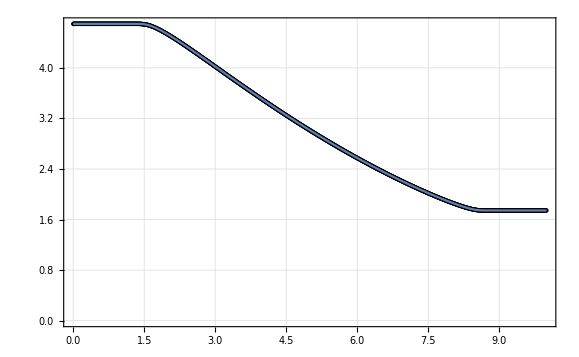

```mathematica
Show[ListPlot[state640, PlotTheme-> "Detailed", PlotStyle-> Black], exactDensity]
```

```mathematica
γ = 7/5;
ρL = 4.696; ρR = 1.744;
uL = 0; uR = 311.92;
pL =404400; pR = 101100;
aL = √((γ pL)/ρL); aR = √((γ pR)/ρR);
f[x_]:=Piecewise[{
{(Tanh[√2 Tan[π x/2]] + 1)/2, -1 < x < 1},
{0, x ≤ -1},
{1, x ≥ 1}}];
p[x_ ] = (pR - pL)f[2(x - 6)/2.5 - 1] + pL;
ρ[x_] := Piecewise[{{ρL, x ≤ 6},{ρL/pL^(5/7)p[x]^(5/7), 6 < x < 8.5},{ρR, x ≥ 8.5}}];
u[x_] := Piecewise[{{uL, x ≤ 6},{uR + (2aR)/(γ-1) - 2/(γ-1)√((γ p[x])/ρ[x]), 6 < x < 8.5},{uR, x ≥ 8.5}}];
```

```mathematica
intermP[x_]:= (pR - pL)(Tanh[√2 Tan[π (2(x - 6)/2.5 - 1)/2]] + 1)/2 + pL;
intermρ [x_]:= ρL/pL^(5/7)intermP[x]^(5/7);
intermU[x_] := uR + (2aR)/(γ-1) - 2/(γ-1)√((γ intermP[x])/intermρ[x]);
sol[x_, t_]:=FindRoot[x == (((2 aL)/(γ - 1))((3 - γ)/4) - ((γ + 1)/4)((2aL)/(γ - 1)(intermP[x0]/pL)^((γ - 1)/(2γ)) - intermU[x0] ))t + x0, {x0, 7.3}];
```

```mathematica
intermP[x_]:= (pR + pL)/2 - (pR - pL)/2 Cos[(2π(x-6))/5];
intermρ [x_]:= ρL/pL^(5/7)intermP[x]^(5/7);
intermU[x_] := uR + (2aR)/(γ-1) - 2/(γ-1)√((γ intermP[x])/intermρ[x]);
```

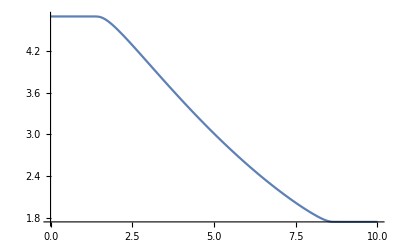

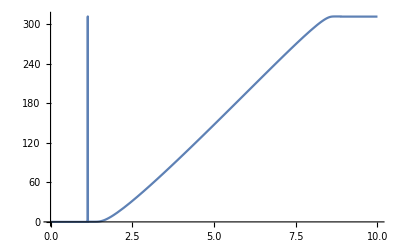

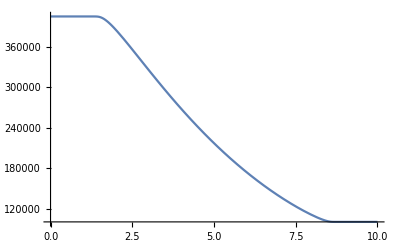

```mathematica
Exactρ[x_, t_] := Piecewise[{
{ρL, x < 6 + t(uL - aL)}, 
{intermρ[x0/.sol[x, t]],  6 + t(uL - aL)≤ x ≤ 8.5 + t(uR - aR) },
{ρR, x > 8.5 + t(uR - aR)}}];
ExactU[x_, t_] := Piecewise[{
{uL, x < 6 + t(uL - aL)}, 
{intermU[x0/.sol[x, t]],  6 + t(uL - aL)≤ x ≤ 8.5 + t(uR - aR) },
{uR, x > 8.5 + t(uR - aR)}}];
ExactP[x_, t_] := Piecewise[{
{pL, x < 6 + t(uL - aL)}, 
{intermP[x0/.sol[x, t]],  6 + t(uL - aL)≤ x ≤ 8.5 + t(uR - aR) },
{pR, x > 8.5 + t(uR - aR)}}];
exactDensity = Plot[Exactρ[x, 0.014], {x, 0, 10}, PlotRange->All]
exactVelocity = Plot[ExactU[x, 0.014], {x, 0, 10}, PlotRange->All]
exactPressure = Plot[ExactP[x, 0.014], {x, 0, 10}, PlotRange->All]
```

```mathematica
NumberOfRows = 3; NumberOfColumns = 5;
Table[0, {i, 1, NumberOfRows}, {j, 1, NumberOfColumns}]//MatrixForm
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

```mathematica
distance = 2;
order = 4;
CC = Table[i Δx, {i, -distance, distance}];
DD = Table[(i Δx^j)/(j!), {i, -distance, distance}, {j, 1, order}];
DTD = Table[Sum[(1/(i!)CC⟦k⟧^i)(1/(j!)CC⟦k⟧^j), {k, 1, Length[CC]}], {i , 1, order}, {j , 1, order}];
DTY = Table[Sum[(U[k - (distance + 1)]- U[0])(1/(i!)CC⟦k⟧^i),{k, 1, Length[CC]}], {i, 1, order}, {j, 1, 1}];
X = LinearSolve[DTD, DTY];
u[x_]:= U[0] + Sum[X⟦i, 1⟧(x^i/(i!)), {i, 1, order}];

(*  ----- OUTPUT -----  *)
 Det[DTD]
 DTD//MatrixForm
 DTY //MatrixForm
 X//MatrixForm
u[Δx]//Simplify
u[Δx/2]//Simplify
u[-Δx/2]//Simplify
```

Δx^20

(10 Δx^2 | 0 | (17 Δx^4)/3 | 0
0 | (17 Δx^4)/2 | 0 | (65 Δx^6)/24
(17 Δx^4)/3 | 0 | (65 Δx^6)/18 | 0
0 | (65 Δx^6)/24 | 0 | (257 Δx^8)/288)

(-2 Δx (U[-2]-U[0])-Δx (U[-1]-U[0])+Δx (-U[0]+U[1])+2 Δx (-U[0]+U[2])
2 Δx^2 (U[-2]-U[0])+1/2 Δx^2 (U[-1]-U[0])+1/2 Δx^2 (-U[0]+U[1])+2 Δx^2 (-U[0]+U[2])
-4/3 Δx^3 (U[-2]-U[0])-1/6 Δx^3 (U[-1]-U[0])+1/6 Δx^3 (-U[0]+U[1])+4/3 Δx^3 (-U[0]+U[2])
2/3 Δx^4 (U[-2]-U[0])+1/24 Δx^4 (U[-1]-U[0])+1/24 Δx^4 (-U[0]+U[1])+2/3 Δx^4 (-U[0]+U[2]))

((U[-2]-8 U[-1]+8 U[1]-U[2])/(12 Δx)
(-U[-2]+16 U[-1]-30 U[0]+16 U[1]-U[2])/(12 Δx^2)
(-U[-2]+2 U[-1]-2 U[1]+U[2])/(2 Δx^3)
(U[-2]-4 U[-1]+6 U[0]-4 U[1]+U[2])/Δx^4)

U[1]

1/128 (3 U[-2]-20 U[-1]+90 U[0]+60 U[1]-5 U[2])

1/128 (-5 U[-2]+60 U[-1]+90 U[0]-20 U[1]+3 U[2])

```mathematica
DD//MatrixForm
Transpose[DD].DD//MatrixForm
```

(-2 Δx | -Δx^2 | -Δx^3/3 | -Δx^4/12
-Δx | -Δx^2/2 | -Δx^3/6 | -Δx^4/24
0 | 0 | 0 | 0
Δx | Δx^2/2 | Δx^3/6 | Δx^4/24
2 Δx | Δx^2 | Δx^3/3 | Δx^4/12)

(10 Δx^2 | 5 Δx^3 | (5 Δx^4)/3 | (5 Δx^5)/12
5 Δx^3 | (5 Δx^4)/2 | (5 Δx^5)/6 | (5 Δx^6)/24
(5 Δx^4)/3 | (5 Δx^5)/6 | (5 Δx^6)/18 | (5 Δx^7)/72
(5 Δx^5)/12 | (5 Δx^6)/24 | (5 Δx^7)/72 | (5 Δx^8)/288)

```mathematica
Transpose[DD].Table[(U[i] - U[0]), {i,-distance, distance} ]//MatrixForm//Simplify
```

(Δx (-2 U[-2]-U[-1]+U[1]+2 U[2])
1/2 Δx^2 (-2 U[-2]-U[-1]+U[1]+2 U[2])
1/6 Δx^3 (-2 U[-2]-U[-1]+U[1]+2 U[2])
1/24 Δx^4 (-2 U[-2]-U[-1]+U[1]+2 U[2]))

```mathematica
distance = 1; order = 2;
DD = Table[(i Δx)^j/(j!), {i, -distance, distance}, {j, 1, order}];
Y = Table[(U[i] - U[0]), {i,-distance, distance}, {j, 1, 1} ];
DTD = Transpose[DD].DD//Simplify;
DTY = Transpose[DD].Y//Simplify;
X = LinearSolve[DTD, DTY];
u[x_]:= U[0] + Sum[X⟦i, 1⟧(x^i/(i!)), {i, 1, order}];

(*  ----- OUTPUT -----  *)
 Det[DTD]
 DTD//MatrixForm
 DTY //MatrixForm
 X//MatrixForm
u[Δx/2]//Simplify
u[-Δx/2]//Simplify
```

Δx^6

(2 Δx^2 | 0
0 | Δx^4/2)

(Δx (-U[-1]+U[1])
1/2 Δx^2 (U[-1]-2 U[0]+U[1]))

((-U[-1]+U[1])/(2 Δx)
(U[-1]-2 U[0]+U[1])/Δx^2)

1/8 (-U[-1]+6 U[0]+3 U[1])

1/8 (3 U[-1]+6 U[0]-U[1])